```mathematica
GetSnapshot[n_]:=ReadList["/Users/nicorivas/Software/BOS2/BOS/build/snapshot_"<>ToString[n]<>".dat",{Number,Number,Number,Number,Number,Number}]
```

```mathematica
nn=Length[FileNames["/Users/nicorivas/Software/BOS2/BOS/build/snapshot_*"]];
```

```mathematica
GetSnapshot[7]
```

{{3.78472,2.5,4.45924}}

```mathematica
ShowSnapshot[n_]:=Row[{
ListPlot[{GetSnapshot[n][[All,{1,2}]],GetSnapshot[n][[All,{4,5}]]},PlotRange->{{0,5},{0,5}},Frame->True,AspectRatio->1,ImageSize->300,PlotMarkers->{Graphics[{Black,Disk[]},ImageSize->300/5*0.5*2],Graphics[{Red,Circle[]},ImageSize->300/5*0.5*2]}],ListPlot[{GetSnapshot[n][[All,{1,3}]],GetSnapshot[n][[All,{4,6}]]},PlotRange->{{0,5},{0,5}},Frame->True,AspectRatio->1,ImageSize->300,PlotMarkers->{Graphics[{Black,Disk[]},ImageSize->300/5*0.5*2],Graphics[{Red,Circle[]},ImageSize->300/5*0.5*2]}],
ListPlot[{GetSnapshot[n][[All,{2,3}]],GetSnapshot[n][[All,{5,6}]]},PlotRange->{{0,5},{0,5}},Frame->True,AspectRatio->1,ImageSize->300,PlotMarkers->{Graphics[{Black,Disk[]},ImageSize->300/5*0.5*2],Graphics[{Red,Circle[]},ImageSize->300/5*0.5*2]}]}]
```

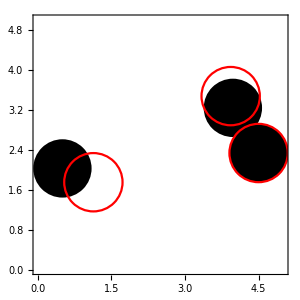
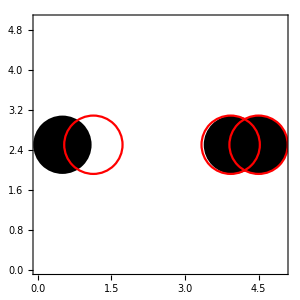
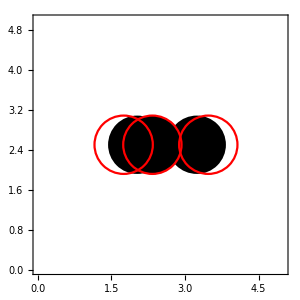

```mathematica
ShowSnapshot[10]
```

```mathematica
nn=Length[FileNames["/Users/nicorivas/Software/BOS2/BOS/build/snapshot_*"]];
Animate[ShowSnapshot[i],{i,0,nn-1,1},DisplayAllSteps->True]
```

```mathematica
nn=Length[FileNames["/Users/nicorivas/Software/BOS2/BOS/build/snapshot_*"]];
Manipulate[ShowSnapshot[i],{i,0,nn-1,1}]
```

```mathematica
Solve[2^2+2^2==x^2]
```

{{x→-2 √2},{x→2 √2}}